WolframAlphaQueryResults

-Graphics3D-

```mathematica
1/2
```

1/2

```mathematica
Underscript[1, 2]
```

1_2

```mathematica
Overscript[234, 1]
```

234^1

```mathematica
∑_(x=0)^∞ Sin[x]/x
```

1+1/2 (-1+π)

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

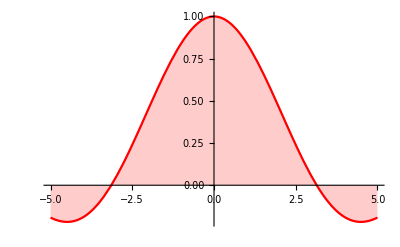

```mathematica
Plot[Sin[x]/x,{x,-5,5},Filling->Axis,PlotStyle->Red]
```

```mathematica
%14
```

## Making interactive models manipulate

```mathematica
Manipulate[Plot[amp fun[freq x],{x,-10,10}],{freq,1,5},{amp,0,5},{fun,{Sin,Cos,Tan}}]
```

## Solver

### DSolver

```mathematica
DSolve[y'[x]== 2x+5,y[x],x]
```

{{y[x]→5 x+x^2+C[1]}}

```mathematica
DSolve[y'[x]== (2y[x]+5)/(x+2),y[x],x]
```

{{y[x]→-5/2+(2+x)^2 C[1]}}

```mathematica
DSolve[y''[x]+2 y'[x] - 8 y[x] == 6 Cos[x],y[x],x]//Simplify
```

{{y[x]→ⅇ^(-4 x) C[1]+ⅇ^(2 x) C[2]-6/85 (9 Cos[x]-2 Sin[x])}}

```mathematica
DSolve[{y'[t] == k (y[t]-T),y[0]==T1},y[t],t]//FullSimplify
```

```mathematica
{{y[t]->T+ⅇ^(k t) (-T+T1)}}
```

{{y[t]→T+ⅇ^(k t) (-T+T1)}}

## Presentations

#### Slide show

## Solver

```mathematica
Solve[{a x^2+b x+c==0},x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
FindRoot[Log[x]==Exp[x]-5,{x,3}]
```

{x→1.71152}

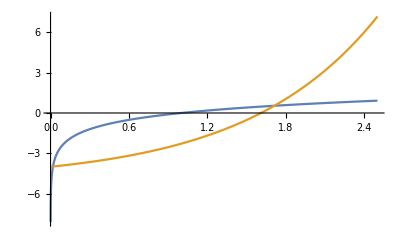

```mathematica
Plot[{Log[x],Exp[x]-5},{x,0,2.5}]
```

```mathematica
Solve[Sin[x]==0.5,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.523599}}

```mathematica
Reduce[Sin[x]==1/2,x]
```

C[1]∈Integers&&(x==π/6+2 π C[1]||x==(5 π)/6+2 π C[1])

```mathematica
Disk[]
```

Disk[{0,0}]

```mathematica
Ω=Disk[];
op = -Laplacian[u[x,y],{x,y}]-1;
bd = DirichletCondition[u[x,y]==0, x≥0];
```

```mathematica
uif = NDSolveValue[{op==0,bd},u,{x,y} ∈ Ω];
```

```mathematica
Plot3D[uif[x,y],{x,y}∈ Ω]
```

-Graphics3D-

```mathematica
!x>2
```

x≤2

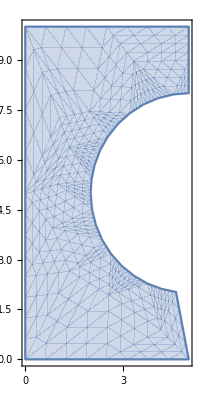

```mathematica
Ω=ImplicitRegion[!((x-5)^2+(y-5)^2≤3^2),{{x,0,5},{y,0,10}}];
RegionPlot[Ω,AspectRatio->Automatic]
```

```mathematica
op=-Laplacian[u[x,y],{x,y}]-20;
```

```mathematica
Subscript[Γ, D]={DirichletCondition[u[x,y]==0, x==0&&8≤y≤10],
DirichletCondition[u[x,y]==100,(x-5)^2+(y-5)^2==3^2]};
uif = NDSolveValue[{op==0,Subscript[Γ, D]},u,{x,y}∈Ω];
```

```mathematica
Plot3D[uif[x,y],{x,y}∈Ω]//Quiet
```

-Graphics3D-